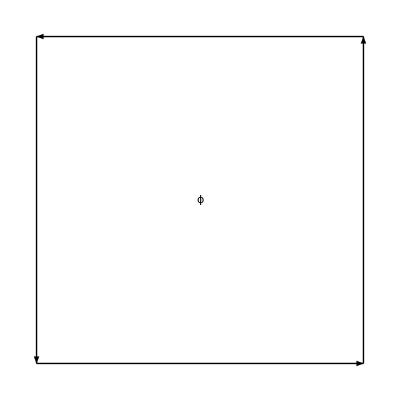

```mathematica
p1=Graphics[{Arrow[{{0,0},{1,0}}],Arrow[{{1,0},{1,1}}],Arrow[{{1,1},{0,1}}],Arrow[{{0,1},{0,0}}],Text[Style["ϕ",Large],{0.5,0.5}]}]
Export["cycle.png",p1];
```

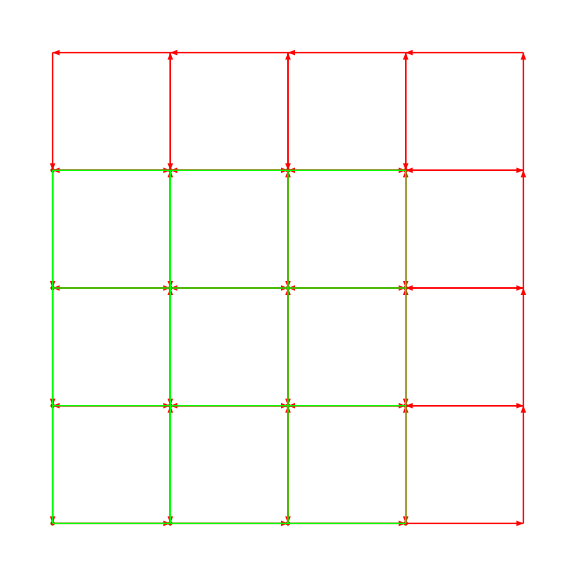

```mathematica
xn=3;yn=3;
t=Table[{x,y},{x,0,xn},{y,0,yn}];
t1=Partition[#,2,1]&/@t;
h=Table[{y,x},{x,0,xn},{y,0,yn}];
h1=Partition[#,2,1]&/@h;
p2=Graphics[{PointSize[Large],Red,Point[#]&/@t,Green,Line[#]&/@t1,Line[#]&/@h1},ImageSize->Large];
cc=Table[{{{0+x,0+y},{1+x,0+y}},{{1+x,0+y},{1+x,1+y}},{{1+x,1+y},{0+x,1+y}},{{0+x,1+y},{0+x,0+y}}},{x,0,xn},{y,0,yn}];
p3=Graphics[{PointSize[Large],Green,Point[#]&/@t,Red,Arrowheads[0.015],Arrow/@cc[[1]],Arrow/@cc[[2]],Arrow/@cc[[3]],Arrow/@cc[[4]]},ImageSize->Large];
p4=Show[{p3,p2}]
Export["la.png",p4];
```

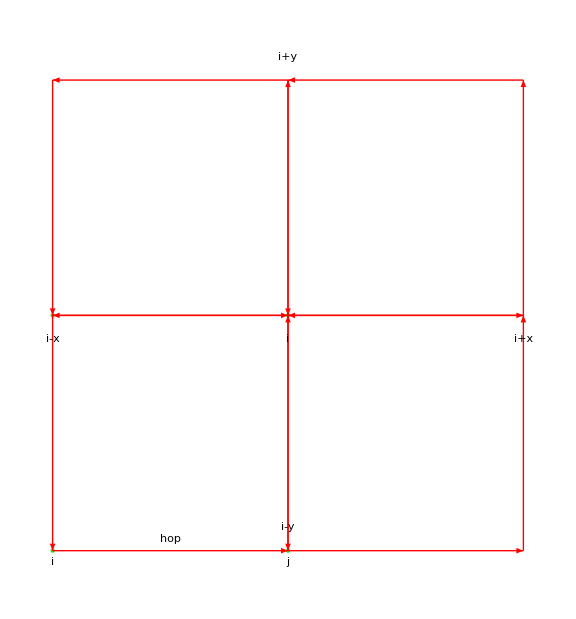

lattice.png

```mathematica
xn=1;yn=1;
t=Table[{x,y},{x,0,xn},{y,0,yn}];
t1=Partition[#,2,1]&/@t;
h=Table[{y,x},{x,0,xn},{y,0,yn}];
h1=Partition[#,2,1]&/@h;
cc=Table[{{{0+x,0+y},{1+x,0+y}},{{1+x,0+y},{1+x,1+y}},{{1+x,1+y},{0+x,1+y}},{{0+x,1+y},{0+x,0+y}}},{x,0,xn},{y,0,yn}];
p2=Graphics[{PointSize[Large],Green,Point[#]&/@t,Red,Arrowheads[0.018],Arrow/@cc[[1]],Arrow/@cc[[2]],Text[Style["i",Black,Large],{0,-0.05}],Text[Style["j",Black,Large],{1,-0.05}],Text[Style["hop",Black,Large,Italic],{0.5,0.05}],Text[Style["i",Black,Large],{1,1-0.1}],Text[Style["i+x",Black,Large],{2,1-0.1}],Text[Style["i-x",Black,Large],{0,1-0.1}],Text[Style["i+y",Black,Large],{1,2+0.1}],Text[Style["i-y",Black,Large],{1,0.1}]},ImageSize->Large]
Export["lattice.png",p2]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["lattice.png"]]]
```